# Schelling model

Based on: http://nifty.stanford.edu/2014/mccown-schelling-model-segregation/

Text from the lecture:
Suppose there are two types of agents: X and O. The two types of agents might represent different races, ethnicity, economic status, etc. Two populations of the two agent types are initially placed into random locations of a neighborhood represented by a grid. After placing all the agents in the grid, each cell is either occupied by an agent or is empty as shown below. 
Now we must determine if each agent is satisfied with its current location. A satisfied agent is one that is surrounded by at least t percent of agents that are like itself. This threshold t is one that will apply to all agents in the model, even though in reality everyone might have a different threshold they are satisfied with. Note that the higher the threshold, the higher the likelihood the agents will not be satisfied with their current location.

For example, if t = 30%, agent X is satisfied if at least 30% of its neighbors are also X. If fewer than 30% are X, then the agent is not satisfied, and it will want to change its location in the grid. For the remainder of this explanation, let’s assume a threshold t of 30%. This means every agent is fine with being in the minority as long as there are at least 30% of similar agents in adjacent cells.

When an agent is not satisfied, it can be moved to any vacant location in the grid. Any algorithm can be used to choose this new location. For example, a randomly selected cell may be chosen, or the agent could move to the nearest available location.

All dissatisfied agents must be moved in the same round. After the round is complete, a new round begins, and dissatisfied agents are once again moved to new locations in the grid. These rounds continue until all agents in the neighborhood are satisfied with their location.

## Definition

```mathematica
CreateGrid[sizex_,sizey_,similar_,groupratio_,empty_]:=Association[{"sizex"->sizex, "sizey"->sizey,"similar_threshold"->similar,"values"->RandomChoice[{empty,(1-empty)groupratio,(1-empty)(1-groupratio)}->{0,1,2},{sizex,sizey}]}];

(* Part with periodic boundaries that also support transition to negative values *)
PeriodicPart[grid_,{i_,j_}]:=Part[grid["values"],##]&@@({Mod[i,grid["sizex"]],Mod[j,grid["sizey"]]}/.(n_?(#<1 &)):>n-1);

GetNeighbors[grid_,{i_,j_}] := Module[{neighbors},
neighbors =Map[{i,j}+#&,Tuples[{-1,0,1},2]];
neighbors = DeleteCases[neighbors,{i,j}];
Return[Map[PeriodicPart[grid,#]&,neighbors]];
];

(* Returns true if the cell is not satisfied with their current neighbors *)
IterateCell[grid_,{i_,j_}]:=Module[{value,neighbors,numberOfNeighbors,satisfaction,updateValue},
value = grid["values"][[i,j]];
If[value ≠ 0,
neighbors = GetNeighbors[grid,{i,j}];
numberOfNeighbors = Count[neighbors,_?((#==1)||(#==2)&)];

If[numberOfNeighbors ≠ 0,
satisfaction = N[Count[neighbors,_?(#==value&)]/numberOfNeighbors],
satisfaction = 0
];
Return[satisfaction≥grid["similar_threshold"]],
Return[True] (* An empty cell will be considered satisfied to avoid moving it *)
];
];

(* Move every unsatisfied nonempty cell *)
IterateCA[grid_]:=Module[{satisfactionMap,emptySlot,unsatisfiedPos,moving,newgrid},
satisfactionMap = Table[IterateCell[grid,{i,j}],{i,1,grid["sizex"]},{j,1,grid["sizey"]}];
unsatisfiedPos = Position[satisfactionMap,False];

If[Length[unsatisfiedPos] ≠ 0,
emptySlot = RandomSample[Position[grid["values"],0]];
moving = RandomChoice[unsatisfiedPos, Length[emptySlot]];

newgrid = grid;
(* Swap values *)
MapThread[
({newgrid[["values",#1[[1]],#1[[2]]]],newgrid[["values",#2[[1]],#2[[2]]]]} = {newgrid[["values",#2[[1]],#2[[2]]]],newgrid[["values",#1[[1]],#1[[2]]]]})&,
{moving,emptySlot}
];

Return[newgrid],
Return[grid]
];
];
```

```mathematica
caEvolution = NestList[IterateCA,CreateGrid[30,30,0.7,0.5,0.1],100];
plt = Map[ArrayPlot[#["values"],ColorRules->{0->White,1->Red,2->Blue},Mesh->All,MeshStyle->Black]&,caEvolution];
```

```mathematica
ListAnimate[plt,SaveDefinitions->True]
```

## Measures

```mathematica
CellHomogeneity[grid_,{i_,j_}]:=Module[{value,neighbors,numberOfNeighbors,satisfaction,updateValue},
value = grid["values"][[i,j]];
If[value ≠ 0,
neighbors = GetNeighbors[grid,{i,j}];
numberOfNeighbors = Count[neighbors,_?((#==1)||(#==2)&)];

If[numberOfNeighbors ≠ 0,
Return[N[Count[neighbors,_?(#==value&)]/numberOfNeighbors]],
Return[Nothing];
],
Return[Nothing];
];
];
MeasureHomogeneity[grid_]:=Module[{homogeneity},
homogeneity = Flatten[Table[CellHomogeneity[grid,{i,j}],{i,1,grid["sizex"]},{j,1,grid["sizey"]}]];
Return[Mean[homogeneity]];
];
```

```mathematica
Needs["AdvancedMapping`"];
```

```mathematica
homogeneitytbl = ProgressParallelTable[{intolerance,MeasureHomogeneity[Nest[IterateCA,CreateGrid[30,30,intolerance,0.5,0.1],100]]},{intolerance,0.1,0.9,0.01}];
```

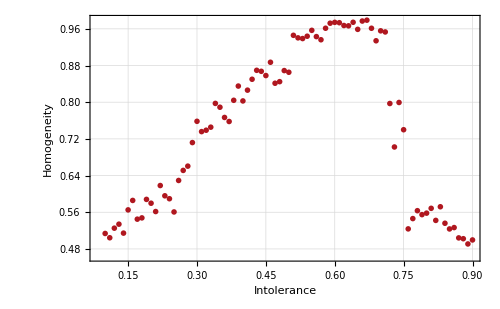

```mathematica
ListPlot[
homogeneitytbl,
ImageSize->500,
PlotRange->Full,
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Intolerance",15], Style["Homogeneity",15]},
BaseStyle->FontSize->13,
PlotStyle->ColorData["Legacy"]["IndianRed"],
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FrameTicks->True
]
```